## Zmax Calculator for Stern-Gerlach

```mathematica
Button["Open Z_max Calculator",ZmaxDialog]
```

Open Z_max Calculator

```mathematica
?Zmax
```

Zmax[B,T_oven] calculates Z_max (in millimeters) for magnetic field B (Tesla) and oven temperature T_oven (Celsius). The expected distance between peaks is twice Zmax.

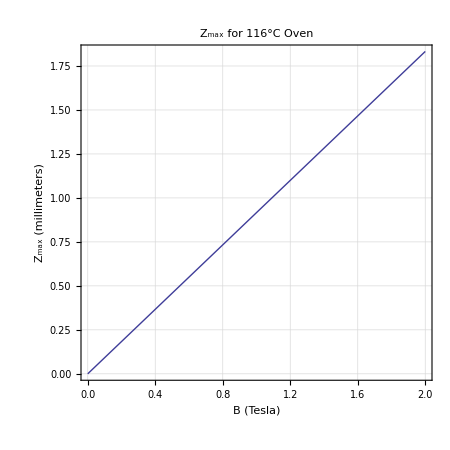

```mathematica
Zplot
```

## Initialization Code

### Constants of nature

```mathematica
Needs["Units`"]
Needs["PhysicalConstants`"]
```

General::obspkg: PhysicalConstants` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
Subscript[μ, B]=Convert[BohrMagneton,Joule/Tesla];
Subscript[k, B]=Convert[BoltzmannConstant,Joule/Kelvin];
T[tempC_]:=ConvertTemperature[1.0tempC,Celsius,Kelvin]Kelvin
```

Convert::temp: Warning: Convert[old,new] converts units of temperature. ConvertTemperature[temp,old,new] converts absolute temperature.

### Dimensions of the apparatus

```mathematica
Subscript[L, 2]=12.7 Centimeter;
Subscript[L, 3]=7.9 Centimeter;
dLogB=1.76 Centimeter^-1;
```

### Zmax as a function of B and Temperature

```mathematica
Zmax[Bz_,Toven_]:=Bz Convert[(Subscript[L, 2](Subscript[L, 2]/2+Subscript[L, 3])Subscript[μ, B])/(6 Subscript[k, B] T[Toven])dLogB  Tesla/(Milli Meter),1]
Zmax::usage="Zmax[B,T_oven] calculates Z_max (in millimeters) for magnetic field B (Tesla) and oven temperature T_oven (Celsius). The expected distance between peaks is twice Zmax."
```

Zmax[B,T_oven] calculates Z_max (in millimeters) for magnetic field B (Tesla) and oven temperature T_oven (Celsius). The expected distance between peaks is twice Zmax.

### The plot

```mathematica
Zplot=Plot[{Zmax[b,116]},{b,0,2},AspectRatio->1,Frame->True,PlotLabel->Style["Z_max for 116°C Oven",Larger],GridLines->Automatic,GridLinesStyle->GrayLevel[.85],PlotStyle->Thick,FrameLabel->{Style["B (Tesla)",Larger,Italic],Style["Z_max (millimeters)",Larger,Italic]},ImageSize->450];
```

### Here is a dynamic calculator of Zmax in a dialog window

```mathematica
ZmaxNotebook=Notebook[{}];
```

```mathematica
ZmaxDialog :=If[ZmaxNotebook===Notebook[{}],
ZmaxNotebook=CreateDialog[
{Manipulate[
Block[{z},
z=Zmax[Bz,Toven];
Grid[{
{Tooltip[Style["Z_max (mm): ",FontFamily->"Helvetica"],"Z_max calculated from the magnetic field and oven temperature"],Tooltip[Style[ToString[ Round[z,.001]],FontFamily->"Helvetica"],"Z_max calculated from the magnetic field and oven temperature (millimeters)"]},{}
},Alignment->{Left,Baseline}](* Grid *)
](* Block *),
Style["Enter Magnetic Field (Tesla) and Oven Temp (Celsius):",Larger],"",
{{Bz,1.0,
"Magnetic Field (Tesla)"}
,ControlType->InputField},
{{Toven,116.,
"Oven Temperature (Celsius)"}
,ControlType->InputField},
AppearanceElements->None](* Manipulate *)
},
Magnification->1.5,
Deployed->True,ShowCellBracket->False,Saveable->False,
WindowSize->All (*,WindowFrame->"Normal",WindowElements->"MagnificationPopUp" *),WindowFloating->False,
WindowTitle->"Zmax Calculator - Physics 7 Stern-Gerlach",
NotebookEventActions->{"WindowClose":>(ZmaxNotebook=Notebook[{}];)}
];,SetSelectedNotebook[ZmaxNotebook]];
```